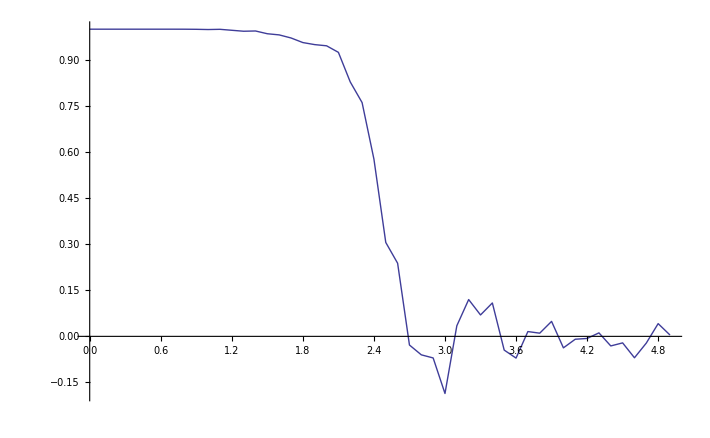

```mathematica
dim=20;
Spin = Table[1,{i,dim},{j,dim}];(*this is the ground state*)
Ver[M_,i_]:=If[i==dim,M[[dim,dim]]*(M[[dim,1]]+M[[1,dim]])+Sum[M[[dim,j]]*(M[[1,j]]+M[[dim,j+1]]),{j,1,dim-1}],M[[i,dim]]*(M[[i+1,dim]]+M[[i,1]])+Sum[M[[i,j]]*(M[[i+1,j]]+M[[i,j+1]]),{j,1,dim-1}]];(*Calculate the energy of one column*)
Energy[M_]:=-Sum[Ver[M,i],{i,1,dim}];(*sum all of the columns to get the energy of the configuration*)
Feromom[N_]:=1/dim^2*∑_(i=1)^dim ∑_(j=1)^dim N[[i,j]];
For[T=0.1;data={{0,1}},T<5,T=T+0.1,
For[time=1;avmom=0;avenergy=0,time<10000,time++, 
coox=RandomInteger[{1,dim}];
cooy=RandomInteger[{1,dim}];
E0=Energy[Spin];
Spin[[coox,cooy]]=- Spin[[coox,cooy]];
If[E0-Energy[Spin]<0,p=RandomReal[];
If[p>Exp[(E0-Energy[Spin])/T],Spin[[coox,cooy]]=- Spin[[coox,cooy]],Spin[[coox,cooy]]= Spin[[coox,cooy]]],Spin[[coox,cooy]]= Spin[[coox,cooy]]
];
avmom=((time-1)*avmom+Feromom[Spin])/time;
avenergy=((time-1)*avenergy+Energy[Spin])/time;
];added={T,N[avmom]};data=Append[data,added]
];
ListLinePlot[data]
```